## Load

```mathematica
(*import the LombScargle module and other photometric tools*)
kernelbooks=FileNames["*.nb",FileNameJoin[{NotebookDirectory[],"kernel"}]];
Map[NotebookEvaluate,kernelbooks];
SetDirectory@NotebookDirectory[];
NotebookSave[]
```

## Import data

```mathematica
fpath=FileNames[{"*.csv","*.txt","*.dat"},"data"]
(*read the files in the data folder*)
```

{data\1143_Catalina.csv}

```mathematica
(*Options@getdata*)
(*uncomment this line if you want to check the options of getdata function*)
```

```mathematica
fname=fpath⟦1⟧;
{db,data0,tspan}=EchoTiming@getdata[fname,"Clipσ"->10,"Crop"->{0,20}];
(*import the light curve data by using getdata function*)
```

Catalina

0.267535

{2005,2006,2007,2008,2009,2010,2011,2012,2013,2014}

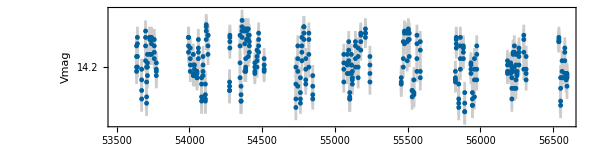

```mathematica
fig0=ploter0[data0,db]
(*check the light curve*)
```

```mathematica
NotebookSave[]
```

## Period-Search

```mathematica
Options[lombscargleF]
(*check the options of lombscargleF function*)
```

{Ofac→8,Hifac→300,Userfreq→{0,0,0},SiderialExclude→0.005}

```mathematica
{freqs,power,period,sig}=EchoTiming@lombscargleF[data0⟦All,{1,2}⟧,data0⟦All,3⟧,"Ofac"->10,"Hifac"->300];
(*search for period*)
period
```

1.61183

0.114989

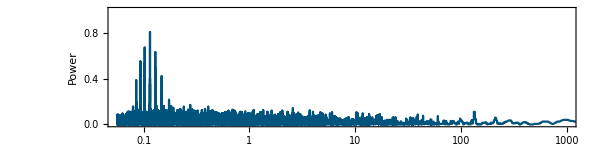

```mathematica
fig1=ploter1[1/freqs,power]
(*examine the LombScargle power*)
```

```mathematica
T0=MaximalBy[data0,#⟦2⟧&]⟦1,1⟧
(*find the MJD at the light curve minimal*)
```

55892.3

```mathematica
pflc=foldcat[data0,2*period,T0];
(*Phase fold the lightcurve. Since this source is an ellipsoidal variable, the true period is double the period found by the LombScargle*)
```

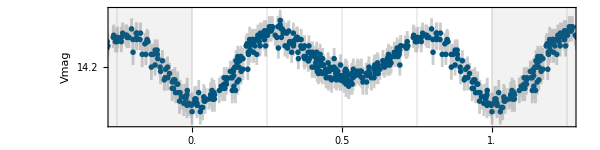

```mathematica
fig2=ploter2[copy2@pflc,db]
```

```mathematica
NotebookSave[]
```

## Export

```mathematica
(*export the results*)
MapThread[Export[FileNameJoin[{NotebookDirectory[],"results",StringJoin[#2,".jpg"]}],Style[#1,Magnification->2]]&,{{fig0,fig1,fig2},{"lightcurve","lombscargle_power","phased_lightcurve"}}]
```

{C:\Astroyi_Teams\ToolBox_Photometry\results\lightcurve.jpg,C:\Astroyi_Teams\ToolBox_Photometry\results\lombscargle_power.jpg,C:\Astroyi_Teams\ToolBox_Photometry\results\phased_lightcurve.jpg}

```mathematica
fname
```

data\1143_Catalina.csv

```mathematica
Export[StringReplace[fname,"data"->"results"],{{"database","period","T0"},{db,2*period,T0}}]
```

results\1143_Catalina.csv

```mathematica
NotebookSave[]
```